```mathematica
g=5-x
bounds={x,2,5}
Integrate[g,bounds]
```

5-x

{x,2,5}

9/2

```mathematica
g=x-1;
bounds={x,1,3};
A=Integrate[g,bounds]
k=1/A
```

2

1/2

(-26+5 ⅇ^3)/ⅇ^4

1.363191

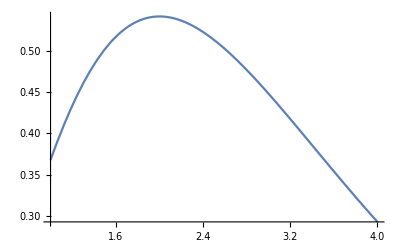

```mathematica
g=x^2 Exp[-x];
bounds={x,1,4};
A=Integrate[g,bounds]
N[A,7] (*This provides 7 significant figures*)
Plot[g,bounds]
```

```mathematica
k=1/A;
f=k*g;
Integrate[f,{x,1,4}]
```

1

```mathematica
EV=Integrate[x f,{x,1,4}]
%//N
Var=Integrate[(x-EV)^2 f,{x,1,4}]
%//N
```

(2 (-71+8 ⅇ^3))/(-26+5 ⅇ^3)

2.40997

(3 (420-422 ⅇ^3+23 ⅇ^6))/((26-5 ⅇ^3)^2)

0.66221

```mathematica
ProbBetween2and3=Integrate[ f,{x,2,3}]//N
```

0.371902

```mathematica
ProbBetween1and3=Integrate[ f,{x,1,3}]//N
```

0.728451

(49 π)/4

38.48451

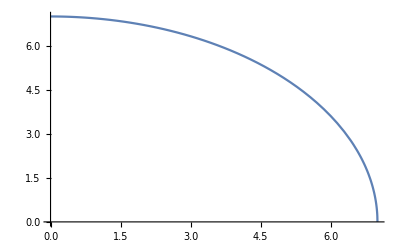

1

28/(3 π)

2.97089

49/4-784/(9 π^2)

3.4238

```mathematica
g=Sqrt[49-x^2];
bounds={x,0,7};
A=Integrate[g,bounds]
N[A,7] (*This provides 7 significant figures*)
Plot[g,bounds]
k=1/A;
f=k*g;
Integrate[f,bounds]
EV=Integrate[x f,bounds]
%//N
Var=Integrate[(x-EV)^2 f,bounds]
%//N
```